```mathematica
kT=4.1; (*pN nm*)
zeta=20;(*drag in pN us/nm*)
dt=0.02; (*timestep in us*)
nstep=1000;  (*number of timesteps*)

externalForce[position_]:=(
Return[0];  (*external force is 0 *)
);

SeedRandom[1];  (* choose a random seed.  If you don't do this, the random seed is always different *)

data=Table[{i dt,0},{i,1,nstep}];  (* data to plot.  We don't need to store it in a text file since we'll be plotting with mathematica*)

x0=0;
x=x0;
Do[
f=externalForce[x];
x+=f dt/zeta;
x+=Sqrt[2 kT dt/zeta]*RandomVariate[NormalDistribution[0,1]];
data[[step,2]]=(x-x0)^2;
,{step,1,nstep}];
```

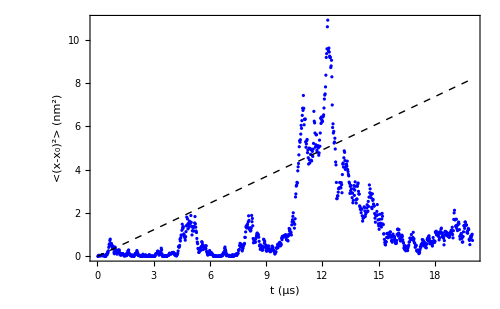

```mathematica
Dcoeff=kT/zeta;
dataplot=ListPlot[data,PlotStyle->Blue];
theoryplot=Plot[2 Dcoeff t,{t,0,20},PlotStyle->{Black,Thick,Dashed}];
combinedplot=Show[
dataplot,theoryplot,
PlotRange->All,
Frame->True,Axes->False,FrameStyle->Thick,
FrameLabel->{"t (μs)","<(x-x_0)^2> (nm^2)"},
ImageSize->500,
BaseStyle->{FontSize->20,FontFamily->"Times New Roman"}
];
Show[combinedplot]
```